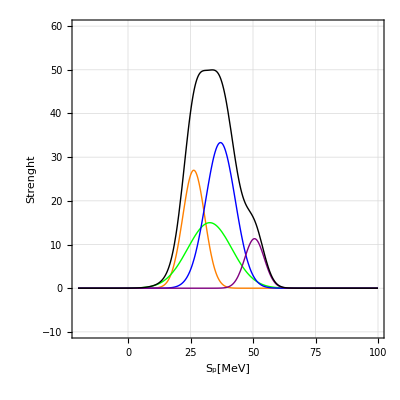

```mathematica
Plot[
{
(*10Exp[-1/2((x-14.7)/2.1)^2],*)
27Exp[-1/2((x-26.3)/4.4)^2],
15Exp[-1/2((x-32.7)/8.8)^2],
50/1.5Exp[-1/2((x-37.0)/5.9)^2],
17/1.5Exp[-1/2((x-50.6)/3.9)^2],
(*10Exp[-1/2((x-14.7)/2.1)^2]+*)27Exp[-1/2((x-26.3)/4.4)^2]+15Exp[-1/2((x-32.7)/8.8)^2]+50/1.5Exp[-1/2((x-37.0)/5.9)^2]+17/1.5Exp[-1/2((x-50.6)/3.9)^2]
}
,{x,-20,100},PlotRange->{-10,60}
,PlotStyle->{(*Red,*)Orange,Green,Blue, Purple,Black},
Axes->False,Frame->True,FrameLabel->{"S_p[MeV]","Strenght"},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dotted],
AspectRatio->1]
```

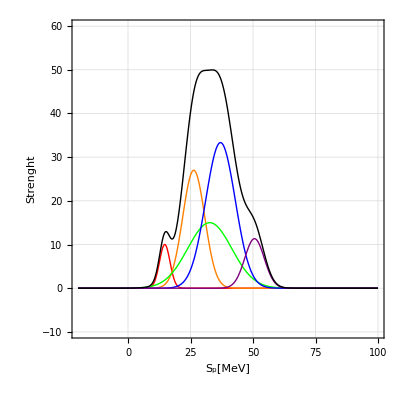

```mathematica
Manipulate[Plot[
{Exp[-1/2((x-13.3)/5)^2],
m1 Exp[-1/2((x-x1)/s1)^2],
m2 Exp[-1/2((x-x2)/s2)^2],
m3 Exp[-1/2((x-x3)/s3)^2],
Exp[-1/2((x-13.3)/5)^2]+m1 Exp[-1/2((x-x1)/s1)^2]+m2 Exp[-1/2((x-x2)/s2)^2]+m3 Exp[-1/2((x-x3)/s3)^2]
}
,{x,-20,100},PlotRange->{-0.5,All}
,PlotStyle->{Red,Orange,Green,Blue, Purple,Black},
Axes->False,Frame->True,FrameLabel->{"S_p[MeV]","Strenght"},
Epilog->{
Text[NIntegrate[Exp[-1/2((x-13.3)/5)^2],{x,13.3-2*5,13.3+2*5}],{0,1}],
Text[NIntegrate[m1 Exp[-1/2((x-x1)/s1)^2],{x,x1-2s1,x1+2s1}],{x1,m1+1}],
Text[NIntegrate[m2 Exp[-1/2((x-x2)/s2)^2],{x,x2-2s2,x2+2s2}],{x2,m2-1}],
Text[NIntegrate[m3 Exp[-1/2((x-x3)/s3)^2],{x,x3-2s3,x3+2s3}],{x3,m3+1}]
},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dotted],
AspectRatio->1],
{m1,1,20},{{x1,26},15,30},{s1,5,10},
{m2,1,20},{{x2,35},20,35},{s2,5,10},
{m3,1,20},{{x3,48},30,50},{s3,5,10}]
```